```mathematica
(* === Load eigenvalue data from Excel === *)
(* Layout: col 1 = s (x-axis for cols 2-17, the 16 gray eigenvalues) *)
(*         col 18 = pink line y,  col 19 = pink line x *)
SetDirectory[NotebookDirectory[]];
raw = Import["../exasp/examples/exact_hubbard_coupling/hubbard_eigs_tracked_physical_20.xlsx", {"Data", 1}];  (* sheet 1 - change if data is elsewhere *)
raw = DeleteCases[raw, {}];  (* drop fully blank rows *)

(* Helper: coerce a cell to a number if possible, else leave it non-numeric *)
toNum[x_] := If[NumericQ[x], x, Quiet[Check[ToExpression[ToString[x]], Null]]];

(* === Gray eigenvalue curves: extracted independently using only cols 1-17 === *)
mainRows = Select[raw, Length[#] >= 17 &];
mainRows = Map[toNum, mainRows[[All, 1 ;; 17]], {2}];
mainRows = Select[mainRows, VectorQ[#, NumericQ] &];
sValues = mainRows[[All, 1]];
grayCurves = Table[Transpose[{sValues, mainRows[[All, i]]}], {i, 2, 17}];

(* === Pink tracked curve: extracted independently using only cols 18-19 === *)
pinkRows = Select[raw, Length[#] >= 19 &];
pinkRows = Map[toNum, pinkRows[[All, {18, 19}]], {2}];  (* {y, x} *)
pinkRows = Select[pinkRows, VectorQ[#, NumericQ] &];
trackedCurve = Transpose[{pinkRows[[All, 2]], pinkRows[[All, 1]]}];  (* {x, y} = {col19, col18} *)
```

```mathematica
(* === Load the second (artificial coupling) dataset - same layout, cols 1-17 only === *)
raw2 = Import["../exasp/examples/exact_hubbard_coupling/hubbard_eigs_tracked_artificial_20.xlsx", {"Data", 1}];  (* sheet 1 - change if data is elsewhere *)
raw2 = DeleteCases[raw2, {}];

mainRows2 = Select[raw2, Length[#] >= 17 &];
mainRows2 = Map[toNum, mainRows2[[All, 1 ;; 17]], {2}];
mainRows2 = Select[mainRows2, VectorQ[#, NumericQ] &];
sValues2 = mainRows2[[All, 1]];
blueCurves = Table[Transpose[{sValues2, mainRows2[[All, i]]}], {i, 2, 17}];
```

```mathematica
(* === Build the plot (styled like the reference figure) === *)
(* raw columns 4 and 11 -> curve indices 3 and 10 (since curve index = column - 1) *)
boldIdx = {3, 10};
restGrayCurves = Delete[grayCurves, List /@ boldIdx];
boldRedCurves = grayCurves[[boldIdx]];
restBlueCurves = Delete[blueCurves, List /@ boldIdx];
boldBlueCurves = blueCurves[[boldIdx]];

grayPlot = ListLinePlot[restGrayCurves, PlotStyle -> Directive[RGBColor[0.75, 0.35, 0.35], Thickness[0.002]]];
boldRedPlot = ListLinePlot[boldRedCurves, PlotStyle -> Directive[RGBColor[0.55, 0.05, 0.05], Thickness[0.005]]];
bluePlot = ListLinePlot[restBlueCurves, PlotStyle -> Directive[RGBColor[0.25, 0.45, 0.75], Thickness[0.002]]];
boldBluePlot = ListLinePlot[boldBlueCurves, PlotStyle -> Directive[RGBColor[0.05, 0.2, 0.5], Thickness[0.005]]];
trackedPlot = ListLinePlot[{trackedCurve}, PlotStyle -> Directive[RGBColor[0.85, 0.05, 0.45], Thickness[0.005]]];

xMajor = Table[{t, NumberForm[t, {1, 1}]}, {t, 0, 1, 0.1}];
xMinor = Table[{t, "", {0.005, 0}}, {t, 0.05, 0.95, 0.1}];
xTop = Join[xMajor /. {t_, lbl_} :> {t, ""}, xMinor];
xBottom = Join[xMajor, xMinor];

yMajor = Range[-2, 10, 2];
yMinor = Table[{y, "", {0.005, 0}}, {y, -1, 9, 2}];
yLeft = yMajor;
yRight = Join[Map[{#, ""} &, yMajor], yMinor];

fig = Show[grayPlot, boldRedPlot, bluePlot, boldBluePlot,
   Frame -> True,
   Axes -> False,
   PlotRange -> {{0, 1}, {-2, 10}},
   PlotRangeClipping -> True,
   FrameLabel -> {Style["s", 16, FontFamily -> "Times New Roman", FontSlant -> Italic], Style["E / ϵ", 16, FontFamily -> "Times New Roman", FontSlant -> Italic]},
   LabelStyle -> {FontFamily -> "Times New Roman", FontSize -> 14, Black},
   FrameStyle -> Black,
   FrameTicks -> {{Join[yMajor, yMinor], yRight}, {xBottom, xTop}},
   PlotRangePadding -> 0,
   ImageSize -> 500,
   AspectRatio -> 0.65
];
```

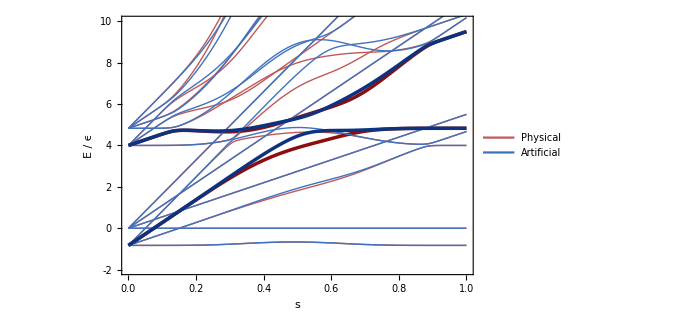

```mathematica
fig = Legended[fig,LineLegend[{RGBColor[0.75,0.35,0.35],RGBColor[0.25,0.45,0.75]},{"Physical","Artificial"}]]
```

```mathematica
(* === Debug check: run this if the pink line is still missing === *)
{Length[mainRows], Length[pinkRows], Length[trackedCurve],
 Min[trackedCurve[[All, 1]]], Max[trackedCurve[[All, 1]]],
 Min[trackedCurve[[All, 2]]], Max[trackedCurve[[All, 2]]]}
```

{101,2001,2001,0.,1.,-0.828427,4.82861}

```mathematica
(* === Export the figure === *)
Export["all_eigenvalues_true_tracked_corrected_both_plot.pdf", fig];
Export["all_eigenvalues_true_tracked_corrected_both_plot.png", fig, ImageResolution -> 300];
```

```mathematica
Head[fig]
```

Legended